## Initialization

```mathematica
$path="D:\\Documents\\aDependence\\";
```

```mathematica
Get["D:\\Documents\\DataDump_MultipleShortRangePotential_5_energyVs2.mx"];
Get["D:\\Documents\\DataDump_MultipleShortRangePotential_5_efV5.mx"];
Get["D:\\Documents\\DataDump_MultipleShortRangePotential_5_efVs2.mx"];
```

```mathematica
Needs["NumericalCalculus`"];
```

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;u0=10^-20;δstart=10^-10;m=1;αSch=2m;
ee={10^-10,10^-9,10^-8,10^-7,10^-6,10^-5,10^-4,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1,3,7,10};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];V1[r_,Fa_]=-α/r+If[0≤r<a,Fa,0];
V4[r_,Ff_,Fg_]=-α/r+Ff E^(-Fg r);
V5[r_,Fi_,Fj_]=-α/r+Fi E^(-Fj r^2);
```

```mathematica
Fa=-2.71562984954227987707220753658717987150651086990482099679916347484158640580824`50.;
```

```mathematica
{Ff,Fg}={-4.20415644616125582469299138439140113373493210258692526366760104908016252690683`50.,1.88979567639491639010430213789778028047296373449456361136288297937037496900499`50.};
```

```mathematica
{Fi,Fj}={Fi,Fj}/.{Fi->-2.647828543053613773374298558957824633572173998851964865568`30.,Fj->1.0017713271893313754426035031926440089474493688810307925058`30.};
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
(*EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,opt1,MaxSteps->Infinity];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.99 SetPrecision[evShifted[[n]],3],1.01 SetPrecision[evShifted[[n]],3]},opt2(*,StepMonitor:>PrintTemporary[e]*)],{n,20}]
]*)
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
Flatten@ParallelMap[EigenEnergySolo[V,αSch,{min,max},{SetPrecision[0.99#,3],SetPrecision[1.01#,3]},{opt1},{opt2}]&,evShifted]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
(*time1=SessionTime[];*)
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
(*time2=SessionTime[];
Print["End with "<>ToString[time2-time1]<>"s"];*)
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
Print[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
EigenEnergySolo[V_,αSch_,{min_,max_},{estart_,eend___},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
(*PrintTemporary[V];*)
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,MaxSteps->steps,(*StepMonitor:>PrintTemporary[{r,u[e][r]}],*)opt1];
(*PrintTemporary[{estart,eend}];*)
time2=SessionTime[];
evnew=e/.#&/@
FindRoot[u[e][min]==0/.sol,{e,estart,eend},opt2(*,StepMonitor:>{time1=time2;time2=SessionTime[];Print[{e,u[e][min]/.sol},"time:",time2-time1,"s"]}*)];
PrintTemporary[evnew];
evnew]
```

```mathematica
lap[f_,r_]:=Simplify[(2 D[f,r])/r+D[f,{r,2}]]
```

```mathematica
enV5=EigenEnergy[V5[r,Fi,Fj],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.65525,-0.180996,-0.0702573,-0.037135,-0.0229255,-0.0155501,-0.0112364,-0.0084974,-0.00665028,-0.005346,-0.00439094,-0.0036707,-0.00311417,-0.00267524,-0.00232297,-0.00203596,-0.00179903,-0.00160118,-0.00143426,-0.00129213}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$673]-u''[r$673]/2==e$672 u[r$673],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$675]-u''[r$675]/2==e$674 u[r$675],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$653]-u''[r$653]/2==e$652 u[r$653],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00534599997654582862426505288713}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$722]-u''[r$722]/2==e$721 u[r$722],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0112364489267084374814933288331}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$740]-u''[r$740]/2==e$739 u[r$740],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0371350177601017527017422082335}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$738]-u''[r$738]/2==e$737 u[r$738],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00849740069775676208320025754822}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$808]-u''[r$808]/2==e$807 u[r$808],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00439093916686959003441001455703}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$878]-u''[r$878]/2==e$877 u[r$878],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00665028253835680722325786499828}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$872]-u''[r$872]/2==e$871 u[r$872],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0229254521760267814103713741141}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$798]-u''[r$798]/2==e$797 u[r$798],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.0155500593971077102983143655342}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$864]-u''[r$864]/2==e$863 u[r$864],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00311416672529010154782299497115}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$1020]-u''[r$1020]/2==e$1019 u[r$1020],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-0.00367070121190102486925525692573}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$1030]-u''[r$1030]/2==e$1029 u[r$1030],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00232296532189673274268339707025}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$1006]-u''[r$1006]/2==e$1005 u[r$1006],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.0026752362615406637405504531914}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$1132]-u''[r$1132]/2==e$1131 u[r$1132],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00179903010214610763436239478604}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$1168]-u''[r$1168]/2==e$1167 u[r$1168],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00143425578620551705900530477619}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$1282]-u''[r$1282]/2==e$1281 u[r$1282],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00160117743104597658934536125435}

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00203595625546321325131664561836}

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00129213828914940868068672015276}

{-1.65524890508386821541551725292}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$736]-u''[r$736]/2==e$735 u[r$736],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.180996164645377719234621562817}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.64782854305361377337429855896 Power[«2»]-Power[«2»]) u[r$796]-u''[r$796]/2==e$795 u[r$796],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{-0.0702572822409696171169025820952}

{-1.65524890508386821541551725292,-0.180996164645377719234621562817,-0.0702572822409696171169025820952,-0.0371350177601017527017422082335,-0.0229254521760267814103713741141,-0.0155500593971077102983143655342,-0.0112364489267084374814933288331,-0.00849740069775676208320025754822,-0.00665028253835680722325786499828,-0.00534599997654582862426505288713,-0.00439093916686959003441001455703,-0.00367070121190102486925525692573,-0.00311416672529010154782299497115,-0.0026752362615406637405504531914,-0.00232296532189673274268339707025,-0.00203595625546321325131664561836,-0.00179903010214610763436239478604,-0.00160117743104597658934536125435,-0.00143425578620551705900530477619,-0.00129213828914940868068672015276}

```mathematica
Export[$path<>"enV5.dat",enV5,"CSV"];
```

```mathematica
enV5=Flatten@Import[$path<>"enV5.dat","CSV"];
```

```mathematica
AbsoluteTiming[efV5=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[PrintTemporary[n];
efunction[[n]]=First@Eigenfunsin[V5[r,Fi,Fj],enV5[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.01},{Exclusions->1}];efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

```mathematica
lapV5=Table[lap[efV5[[n]]/(√(4π)r),r],{n,20}];
```

Calculation

### Determine c_1a

```mathematica
δexpminus10=δ50e[10^-10,V5[r,Fi,Fj]];
δexpminus9=δ50e[10^-9,V5[r,Fi,Fj]];
δexpminus5=δ50e[10^-5,V5[r,Fi,Fj]];
δ50V=δ50[V5[r,Fi,Fj]];
```

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00031483920544494805272898283599555078154800410878) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00099560881674277120935653241123783590452993417866) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/100000+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.09937038001119351020256797027129594018126744004) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.01+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.001+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.22149) is less than WorkingPrecision (50.).

{0.01,-0.88477238714447337423379456595431816599593742697693}    0.7343827

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.879537) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.03+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.031477968606915099061992449255552174135079712824) is less than WorkingPrecision (50.).

{0.001,-0.72139357822496498258162694857794932533087720638821}    0.7968835

{1/1000000,-0.03146757800397505811656613088414195696019756216533}    0.8437582

NDSolve::precw: The precision of the differential equation ({{2 (0.003+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/100000+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00099560881674277120935653241123783590452993417866) is less than WorkingPrecision (50.).

{1/1000000000,-0.00099560848778156251424398110282198110060624252552188}    1.046886

NDSolve::precw: The precision of the differential equation ({{2 (1/100000000+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.09937038001119351020256797027129594018126744004) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-230.949) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.20081) is less than WorkingPrecision (50.).

{1/100000,-0.099045227580948256732764416182565090450579432793947}    0.546881

{0.003,-1.5664663903869268685896834390391042280003947298}    0.609382

{0.03,-0.1981741573193586130044202226193753943474697676629}    0.703136

NDSolve::precw: The precision of the differential equation ({{2 (1/10000+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.007+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{2 (0.07+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0031483861694084166627269799557818401791592660796) is less than WorkingPrecision (50.).

{1/100000000,-0.0031483757668503162111546446654775728469412168837478}    0.593755

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0186489) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.30818825094659949470007188978866515189668642629) is less than WorkingPrecision (50.).

{0.007,0.018646769292047794981511846765042973955750138277754}    0.54688

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1/10000,-0.29895191927331823999104333018850765889282054602626}    0.640631

NDSolve::precw: The precision of the differential equation ({{2 (0.3+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.826203) is less than WorkingPrecision (50.).

{0.07,0.69051521179668764801443614336171061496264949560835}    0.593757

NDSolve::precw: The precision of the differential equation ({{2 (0.1+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0099559020429325254060863228656067778276962538159) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1/10000000,-0.0099555731195386930091129145583138837153174338935845}    0.562507

NDSolve::precw: The precision of the differential equation ({{2 (7+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.13569) is less than WorkingPrecision (50.).

{0.1,-0.13486669995048488543524342013755838904424323553792}    0.8593954

FindRoot::precw: The precision of the argument function (Tan[δ]==0.658953) is less than WorkingPrecision (50.).

{0.3,0.5826435461506521918468045628133048554221678434289}    1.078137

NDSolve::precw: The precision of the differential equation ({{2 (0.7+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==37.9047165698941859119313591842656410710642719) is less than WorkingPrecision (50.).

{1,1.54442050380934932144656226837272817865335610935}    1.531266

NDSolve::precw: The precision of the differential equation ({{2 (3+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.58896) is less than WorkingPrecision (50.).

{0.7,-1.0090796325907611764960197051758558014001221586454}    1.171888

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0180244851279942812378421357223931852835461207) is less than WorkingPrecision (50.).

{3,0.018022533564419210332977355465636235942804753189716}    2.4219

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.2150313073403339282631746415446491949120357489) is less than WorkingPrecision (50.).

{7,-0.8821731402000624760311667322578990300062707277356}    3.765664

NDSolve::precw: The precision of the differential equation ({{2 (10+2.64782854305361377337429855896 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.501615556104347573238033190121613739780221829) is less than WorkingPrecision (50.).

{10,-1.1905126609337501262153145774697705334113581625016}    3.562537

```mathematica
nRange=20;
```

```mathematica
hhhc1[en_,a_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[c1_]:=N[hhhc1[10^-10,a,c1]-δexpminus10,8];
Determinec1[a_,{start_,end___},opt___]:=Module[{findroot},
Print[a];
findroot=FindRoot[hhhc1[10^-10,a,c1]==δexpminus10,{c1,start,end},opt];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1a={};
```

```mathematica
Module[{table},
table=ParallelTable[Block[{c1,a},
a=10^loga;
c1=Determinec1[a,{0},{MaxIterations->If[a>10,200,100],PrecisionGoal->10,WorkingPrecision->50}];
{a,c1}],{loga,DeleteDuplicates[Join[Range[2,1,-0.02],Range[1,0,-0.02],Range[0,-1,-0.1],Range[-1,-3,-0.4]]]}];
c1a=DeleteDuplicates@Sort[c1a~Join~table]
]
```

100.

63.0957

39.8107

25.1189

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.001697979230839371255597111761846442876101896285) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007080825568615731125747527397203589864186214156) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000691533870131827447159790285729474411013289881625) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.001697979230839371255597111761846442876101896285) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-1.49951×10^-11 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007080825568615731125747527397203589864186214156) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-9.46129×10^-12 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000839156082226654886369679990199569147367450379916) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000691533870131827447159790285729474411013289881625) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-2.37657×10^-11 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0016979789639632308645647528601905605311581397931) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000691533870525243164726960710465842933993016136078) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007080825572758629025120772111693799303613160617) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000839156082226654886369679990199569147367450379916) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-3.76661×10^-11 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000839156083757748849528015936859001896362469132464) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

0.68168881964882347485205782086579984208599873943229

60.256

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-6.1357516401184839761810336690584962692047273151159

95.4993

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-5.3150917360535099570325065804158659196632302629492

91.2011

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-3.946067543701306667578561978288497396954656593061

38.0189

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-22.412127340665092235289884756924818649230981702946

23.9883

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-4.5300958731380253109097539597876572467510271802642

87.0964

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-49.02260516801860686323720100801907057137297984982

57.544

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-3.2762182706759724929501737963168510219664252892435

36.3078

-3.7788854923047240267332366140983526651173314443702

83.1764

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-8.0704505966954334518085687128259903535480290076549

22.9087

-3.0596344949411994420335286995319379831393290872233

79.4328

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-10.351661577713896311985332935584462089873003520782

54.9541

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-2.6275604671372344321690715652808064091094944155797

34.6737

-2.370563944257693502554821296001241520560984840476

75.8578

-25.042118260013306621312980956836951219427351298173

52.4807

-1.7099368572519809247818164566024717679721355283883

72.4436

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-21.156005548137448541340363883490651490752168170645

21.8776

-1.9977497178617900019737496994745961966425386088119

33.1131

-1.0760531105195441144205844951210071547173215480981

69.1831

-8.5423739906903014635672943232813265528665259279632

50.1187

-0.46724449504057330221758277649426955934835414428284

66.0693

-1.3844559470482801772809365010890549098570652961747

31.6228

-6.8734441039855487279309947586074639076124876058857

20.893

0.11813003037081111902678667181994506140645020969155

15.8489

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000652910489955880113546166917628975402602190245665) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000652910489955880113546166917628975402602190245665) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-5.96967×10^-11 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00065291049039470811409662598153906458706963875939) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-22.309226245001997510436344333578576651548099334281

47.863

-0.78537390104715842517816261969402893376468510809717

30.1995

-6.2940694701281073510890904892366122937370321253484

19.9526

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-2.9223020363004295340010400573099545223890627539111

15.1356

-6.884514180409305814892083855055592668991721770273

45.7088

-0.19823858633819345154631455702073938602431057986982

28.8403

-5.7236147215116310181278666427038871341660810123388

19.0546

-6.1063165679629293909287757958251810768980335011894

43.6516

0.37915367039671232142024053827514980949163557032807

27.5423

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-2.3599472097492393258613655828667790270025553592264

14.4544

-5.3587559718474303891463718752184041292797688804799

41.6869

-5.1594410994930474273192092928592591279536803206567

18.197

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-1.7944002989826515378146792307369579053616106080968

13.8038

-4.6394608030139089354270208616052028420102987495726

10.

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000848575489469291939497592549879868890656703718613) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000848575489469291939497592549879868890656703718613) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-9.46129×10^-11 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000848575490619253753998743047466437804865337191654) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-40.608537134674351226803333681637032484226771874707

26.3027

-4.5991571203562468452218098883257618384788156622165

17.378

-1.2252563920165366069278478382652032706372935500818

13.1826

-23.117339433600572831508094256163987834948114179588

6.30957

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007058381524771803805621294508526919277259435239) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007058381524771803805621294508526919277259435239) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-1.49951×10^-10 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007058381526560559240814728520309971721314179699) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-4.0406628010180836579243161884156373877402534944266

16.5959

-0.65238271867153710954443736228612083593303269401575

12.5893

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-36.094876530764156671052822693892109500845427616503

9.54993

-0.075867892928852991519430275061546167845547087065466

12.0226

-3.4821853206565807076398830212193640555771902180443

3.98107

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000621578146167682903229914061418522311799381625457) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000621578146167682903229914061418522311799381625457) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-2.37657×10^-10 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000621578146508317488428220163767037076939316116899) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-9.2257540416864530513070857889779038387909060325826

6.0256

0.50402856410212293398204696451082634901173989223781

11.4815

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-13.257408184303036376704190516720859266747812832715

9.12011

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-4.0970184671615790035747704135667437085661389526183

3.80189

-14.870060509618294754370954264806084494889753047638

10.9648

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-36.781904628130527177879809009232913700398819815261

5.7544

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-12.837406056325732200177094309893359642439636392194

8.70964

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-3.5519531654881177056172309778752182932899943319784

3.63078

-14.476462371028111138778746518834438299671382602374

10.4713

-12.410126658235680545707927494978440266555900816988

8.31764

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-8.256881927694071887826782147160694711775537035233

5.49541

-36.041283782374046809037320499058823223696878347398

2.51189

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.008577889898683544697998544264129055361964091685) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.008577889898683544697998544264129055361964091685) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-3.76661×10^-10 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.008577887967918849532975581523052115611852350512) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-11.975476024501574260006746618553066030010846314293

7.94328

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-3.0019784437700269429476059416111806843353216640976

3.46737

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

1.5716809409589726257290450906044404823867885641346

2.39883

-7.7612098568668838775150334570461286091742550718778

5.24807

-11.533574645598253526517174508629437116684535216409

7.58578

-2.4467776210464852501590995093007493555717688340023

3.31131

-7.2577262434167771906767450798246419296430587131415

5.01187

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-191.18858143548435470791038687733559713598478224582

2.29087

-11.084729947933217557957578396882944402551128120037

7.24436

-1.8860994920955643596974526636404301347532674881785

3.16228

-10.629326378710098024582738236546586420788003055085

6.91831

-6.7465860326552332289298022117965707719799875029928

4.7863

-1.3199295569769583065673664927269207806715385178196

3.01995

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-39.233113223785362727157698126035162728078310159447

2.18776

-10.167673360852245234016395568848274352791172248092

6.60693

-6.2282725410130360994261649453429945690170686117906

4.57088

-0.74860325492445981255324483508666710293935359771286

2.88403

-108.40726473197257887163073898282624810960232639962

2.0893

-9.6998718395317687352492721903241350420496859688328

1.65959

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000836887588257256615862746155046428433718260457783) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000836887588257256615862746155046428433718260457783) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-5.70099×10^-10 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000836887588665527541510154229912604182576454104279) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-5.7034890344486090731137678378740220285359023194894

4.36516

-0.1728204274484153378265821779724610246529596552941

2.75423

-39.325276922815494455293666728305265915483761865952

1.99526

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-233.58515105223080244257492238841650041192946909122

1.58489

0.40645809093972388294557545726673356789006701057246

2.63027

-5.172985454364275125399375082724483793852069063794

4.16869

-39.319795891105683792943802326473288917024229485147

1.90546

0.98822064114613588204378970216596761480181311697323

1.09648

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000761089367901094246503744926379405179725908289082) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000761089367901094246503744926379405179725908289082) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-8.6288×10^-10 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000761089368022156930929276732532001698633813955792) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-4.6373779239585316317209293680724614836165741686024

0.199526

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000689587971241520645525842660423816735852021610647) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000689587971241520645525842660423816735852021610647) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-4.74188×10^-9 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000689587971259847355107659603072979101828654726458) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-238.85279687481812159948910466209746070523345373722

1.51356

-218.05900431492836881520026836202643480652347180769

1.8197

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-48.458006572060134836005670186967158023159623623045

0.158489

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-297.21512658721454355776232425374344668054039787755

1.04713

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-124.03064910656653256191678452860214756485826649083

1.44544

-223.27531076167884784361173299721702553562684406142

1.7378

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-55.058584529206511100527065463294490699206068393331

0.125893

-126.38097392870714728568067420092634049906803878074

1.38038

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-307.27106969213178215111361244130417882381274769296

1.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-64.93043035765038111289622154024926079787446986382

0.1

-228.42782339743336322052490653964441604956222538013

-128.97841766045592736635307187084263197442688710096

1.31826

-78.82941777844584395579673587511822957918909303076

0.0398107

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-317.96535077335579089591514337827808687665485460049

0.794328

-202.00270699775871272013557262992868805012713906427

0.0158489

-131.84791452169400755239279400307122882854156203944

1.25893

-181.4388952153539816490937691245425390752658534916

0.630957

-561.04012040155103831087713636584803920855915246301

0.00630957

-135.00351520870358697630029451420205640442477970119

1.20226

-48.309032519741826739598519765858557170102888928003

0.501187

-138.45078199128054177272478082470100511383179219388

1.14815

-47.225417482819106354139176580025665055994716436147

0.398107

-44.700579626201472066691254691412153947740245468746

0.316228

-287.80439662051079865573594369255411924875265317063

-43.476575235813393321184936937040242555332314965631

0.251189

-44.66630577248957766662919884661446555664475986659

-2.9802777135181724235679645573782181600108717210768×10^-7

0.00251189

-2.9802777135181724235679645573782181600108717211933×10^-7

0.001

-2.980277713518172423567964557378218160010871721212×10^-7

{{0.001,-2.980277713518172423567964557378218160010871721212×10^-7},{0.00251189,-2.9802777135181724235679645573782181600108717211933×10^-7},{0.00630957,-2.9802777135181724235679645573782181600108717210768×10^-7},{0.0158489,-561.04012040155103831087713636584803920855915246301},{0.0398107,-202.00270699775871272013557262992868805012713906427},{0.1,-78.82941777844584395579673587511822957918909303076},{0.125893,-64.93043035765038111289622154024926079787446986382},{0.158489,-55.058584529206511100527065463294490699206068393331},{0.199526,-48.458006572060134836005670186967158023159623623045},{0.251189,-44.66630577248957766662919884661446555664475986659},{0.316228,-43.476575235813393321184936937040242555332314965631},{0.398107,-44.700579626201472066691254691412153947740245468746},{0.501187,-47.225417482819106354139176580025665055994716436147},{0.630957,-48.309032519741826739598519765858557170102888928003},{0.794328,-181.4388952153539816490937691245425390752658534916},{1.,-317.96535077335579089591514337827808687665485460049},{1.04713,-307.27106969213178215111361244130417882381274769296},{1.09648,-297.21512658721454355776232425374344668054039787755},{1.14815,-287.80439662051079865573594369255411924875265317063},{1.20226,-138.45078199128054177272478082470100511383179219388},{1.25893,-135.00351520870358697630029451420205640442477970119},{1.31826,-131.84791452169400755239279400307122882854156203944},{1.38038,-128.97841766045592736635307187084263197442688710096},{1.44544,-126.38097392870714728568067420092634049906803878074},{1.51356,-124.03064910656653256191678452860214756485826649083},{1.58489,-238.85279687481812159948910466209746070523345373722},{1.65959,-233.58515105223080244257492238841650041192946909122},{1.7378,-228.42782339743336322052490653964441604956222538013},{1.8197,-223.27531076167884784361173299721702553562684406142},{1.90546,-218.05900431492836881520026836202643480652347180769},{1.99526,-39.319795891105683792943802326473288917024229485147},{2.0893,-39.325276922815494455293666728305265915483761865952},{2.18776,-108.40726473197257887163073898282624810960232639962},{2.29087,-39.233113223785362727157698126035162728078310159447},{2.39883,-191.18858143548435470791038687733559713598478224582},{2.51189,1.5716809409589726257290450906044404823867885641346},{2.63027,0.98822064114613588204378970216596761480181311697323},{2.75423,0.40645809093972388294557545726673356789006701057246},{2.88403,-0.1728204274484153378265821779724610246529596552941},{3.01995,-0.74860325492445981255324483508666710293935359771286},{3.16228,-1.3199295569769583065673664927269207806715385178196},{3.31131,-1.8860994920955643596974526636404301347532674881785},{3.46737,-2.4467776210464852501590995093007493555717688340023},{3.63078,-3.0019784437700269429476059416111806843353216640976},{3.80189,-3.5519531654881177056172309778752182932899943319784},{3.98107,-4.0970184671615790035747704135667437085661389526183},{4.16869,-4.6373779239585316317209293680724614836165741686024},{4.36516,-5.172985454364275125399375082724483793852069063794},{4.57088,-5.7034890344486090731137678378740220285359023194894},{4.7863,-6.2282725410130360994261649453429945690170686117906},{5.01187,-6.7465860326552332289298022117965707719799875029928},{5.24807,-7.2577262434167771906767450798246419296430587131415},{5.49541,-7.7612098568668838775150334570461286091742550718778},{5.7544,-8.256881927694071887826782147160694711775537035233},{6.0256,-36.781904628130527177879809009232913700398819815261},{6.30957,-9.2257540416864530513070857889779038387909060325826},{6.60693,-9.6998718395317687352492721903241350420496859688328},{6.91831,-10.167673360852245234016395568848274352791172248092},{7.24436,-10.629326378710098024582738236546586420788003055085},{7.58578,-11.084729947933217557957578396882944402551128120037},{7.94328,-11.533574645598253526517174508629437116684535216409},{8.31764,-11.975476024501574260006746618553066030010846314293},{8.70964,-12.410126658235680545707927494978440266555900816988},{9.12011,-12.837406056325732200177094309893359642439636392194},{9.54993,-13.257408184303036376704190516720859266747812832715},{10.,-36.094876530764156671052822693892109500845427616503},{10.4713,-36.041283782374046809037320499058823223696878347398},{10.9648,-14.476462371028111138778746518834438299671382602374},{11.4815,-14.870060509618294754370954264806084494889753047638},{12.0226,0.50402856410212293398204696451082634901173989223781},{12.5893,-0.075867892928852991519430275061546167845547087065466},{13.1826,-0.65238271867153710954443736228612083593303269401575},{13.8038,-1.2252563920165366069278478382652032706372935500818},{14.4544,-1.7944002989826515378146792307369579053616106080968},{15.1356,-2.3599472097492393258613655828667790270025553592264},{15.8489,-2.9223020363004295340010400573099545223890627539111},{16.5959,-3.4821853206565807076398830212193640555771902180443},{17.378,-4.0406628010180836579243161884156373877402534944266},{18.197,-4.5991571203562468452218098883257618384788156622165},{19.0546,-5.1594410994930474273192092928592591279536803206567},{19.9526,-5.7236147215116310181278666427038871341660810123388},{20.893,-6.2940694701281073510890904892366122937370321253484},{21.8776,-6.8734441039855487279309947586074639076124876058857},{22.9087,-21.156005548137448541340363883490651490752168170645},{23.9883,-8.0704505966954334518085687128259903535480290076549},{25.1189,-22.412127340665092235289884756924818649230981702946},{26.3027,-23.117339433600572831508094256163987834948114179588},{27.5423,-40.608537134674351226803333681637032484226771874707},{28.8403,0.37915367039671232142024053827514980949163557032807},{30.1995,-0.19823858633819345154631455702073938602431057986982},{31.6228,-0.78537390104715842517816261969402893376468510809717},{33.1131,-1.3844559470482801772809365010890549098570652961747},{34.6737,-1.9977497178617900019737496994745961966425386088119},{36.3078,-2.6275604671372344321690715652808064091094944155797},{38.0189,-3.2762182706759724929501737963168510219664252892435},{39.8107,-3.946067543701306667578561978288497396954656593061},{41.6869,-4.6394608030139089354270208616052028420102987495726},{43.6516,-5.3587559718474303891463718752184041292797688804799},{45.7088,-6.1063165679629293909287757958251810768980335011894},{47.863,-6.884514180409305814892083855055592668991721770273},{50.1187,-22.309226245001997510436344333578576651548099334281},{52.4807,-8.5423739906903014635672943232813265528665259279632},{54.9541,-25.042118260013306621312980956836951219427351298173},{57.544,-10.351661577713896311985332935584462089873003520782},{60.256,-49.02260516801860686323720100801907057137297984982},{63.0957,0.68168881964882347485205782086579984208599873943229},{66.0693,0.11813003037081111902678667181994506140645020969155},{69.1831,-0.46724449504057330221758277649426955934835414428284},{72.4436,-1.0760531105195441144205844951210071547173215480981},{75.8578,-1.7099368572519809247818164566024717679721355283883},{79.4328,-2.370563944257693502554821296001241520560984840476},{83.1764,-3.0596344949411994420335286995319379831393290872233},{87.0964,-3.7788854923047240267332366140983526651173314443702},{91.2011,-4.5300958731380253109097539597876572467510271802642},{95.4993,-5.3150917360535099570325065804158659196632302629492},{100.,-6.1357516401184839761810336690584962692047273151159}}

```mathematica
Export[$path<>"c1aV5.dat",c1a,"CSV"];
```

```mathematica
c1a=Import["D:\\Documents\\aDependence\\c1aV5.dat","CSV"];
```

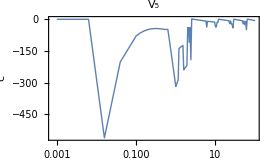

```mathematica
ListLogLinearPlot[c1a,ImageSize->270,Frame->True,Joined->True,PlotRange->All,Axes->False,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{"c",None},{"a",None}},PlotStyle->Thick,PlotLabel->Style["V_5",15],RotateLabel->False,FrameTicksStyle->{{{Bold,11},{}},{{Bold,11},{}}}]
(*Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\Plot_c1_veus_a.eps",%];*)
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
a=1;
```

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus9},{{c2,-40},{d1,3}},MaxIterations->100,WorkingPrecision->30,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00024941294426371440287759844236422165553196081091) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00078871263141617024602877422370586475283010401903) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00024941294426371440287759844236422165553196081091) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{-36.8831922520488512839200149964,5.37946267648713941445379030896,0.000048245581,0.00015256595}

{-41.7219891488876528785321291598,1.34566522054514811207156081637,0.00001554593,0.000049160558}

{-41.3821787806167986580039199155,1.48081181588428463099668430721,5.4579032×10^-7,1.7259401×10^-6}

{-41.3768886575132195798410925884,1.48029474852003801559555519783,7.4301508×10^-10,2.3487141×10^-9}

{-41.3769512623022226071165181317,1.48024194961603734280177244339,-3.0630071×10^-15,-9.161678×10^-13}

{-41.3769324203573853455535183167,1.48025600755064388754886901339,1.3392817×10^-13,-4.8296096×10^-13}

{-41.376932420357381394835402321,1.48025600755064683487522326888,1.3392817×10^-13,-4.8296096×10^-13}

{-41.3769324203573815266764409572,1.48025600755064673651338462777,1.3392817×10^-13,-4.8296096×10^-13}

{-41.3769324203573860114616029794,1.48025600755064339061164367699,1.3392817×10^-13,-4.8296096×10^-13}

{-41.3770020336330035880697232541,1.4802040747276230972662590679,2.9457015×10^-13,2.5024135×10^-14}

{-41.3769979606637325885655697484,1.48020711307286777162940646884,2.6502954×10^-13,-6.8390936×10^-14}

{-41.3769997996464881835648360734,1.48020574106852906014836072674,2.5840165×10^-13,-8.935042×10^-14}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

{-41.3769997996464881835648360733,1.48020574106852906014836072679}

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.46519,-0.18278,-0.0704256,-0.0371692,-0.0229357,-0.0155539,-0.0112382,-0.00849826,-0.00665075,-0.00534627,-0.0043911,-0.00367081,-0.00311424,-0.00267528,-0.002323,-0.00203598,-0.00179905,-0.00160119,-0.00143427,-0.00129214}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$854]-u''[r$854]/2==e$853 u[r$854],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1172]-u''[r$1172]/2==e$1171 u[r$1172],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1404]-u''[r$1404]/2==e$1403 u[r$1404],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1300]-u''[r$1300]/2==e$1299 u[r$1300],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0371692169436628936433917867709}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1228]-u''[r$1228]/2==e$1227 u[r$1228],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00534626902950431127738123945136}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1448]-u''[r$1448]/2==e$1447 u[r$1448],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0229356945829587723666154636539}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1284]-u''[r$1284]/2==e$1283 u[r$1284],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.0112381718461354110738179614055}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1558]-u''[r$1558]/2==e$1557 u[r$1558],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0155539407576502234390353534216}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1344]-u''[r$1344]/2==e$1343 u[r$1344],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0084982576130632855037793286084}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1620]-u''[r$1620]/2==e$1619 u[r$1620],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00439110366993289363567150763646}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1600]-u''[r$1600]/2==e$1599 u[r$1600],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{-0.00311423641315441521148749791304}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1414]-u''[r$1414]/2==e$1413 u[r$1414],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00267528392834665967917961232085}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1548]-u''[r$1548]/2==e$1547 u[r$1548],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-0.00367080632701696886585475589417}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1770]-u''[r$1770]/2==e$1769 u[r$1770],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00665074688977182722711421595391}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1784]-u''[r$1784]/2==e$1783 u[r$1784],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00232299881260609958808458915997}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1690]-u''[r$1690]/2==e$1689 u[r$1690],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.0017990477797848766487628268749}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1904]-u''[r$1904]/2==e$1903 u[r$1904],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00143426581855186800466560951286}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1918]-u''[r$1918]/2==e$1917 u[r$1918],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00160119064190389155128879688607}

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00129214601794152124292028699125}

{-1.46519444532706110446965721253}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$910]-u''[r$910]/2==e$909 u[r$910],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.0020359803403380249186919261358}

{-0.182780371354178358099564821575}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$966]-u''[r$966]/2==e$965 u[r$966],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{-0.0704256294233960810980450764517}

{-1.46519444532706110446965721253,-0.182780371354178358099564821575,-0.0704256294233960810980450764517,-0.0371692169436628936433917867709,-0.0229356945829587723666154636539,-0.0155539407576502234390353534216,-0.0112381718461354110738179614055,-0.0084982576130632855037793286084,-0.00665074688977182722711421595391,-0.00534626902950431127738123945136,-0.00439110366993289363567150763646,-0.00367080632701696886585475589417,-0.00311423641315441521148749791304,-0.00267528392834665967917961232085,-0.00232299881260609958808458915997,-0.0020359803403380249186919261358,-0.0017990477797848766487628268749,-0.00160119064190389155128879688607,-0.00143426581855186800466560951286,-0.00129214601794152124292028699125}

```mathematica
Export[$path<>"a="<>ToString[a]<>"c2d1V5.dat",energyVs2,"CSV"];
```

```mathematica
Import["D:\\Documents\\aDependence\\a=1c2d1V5.dat"];
```

```mathematica
Abs@((energyVs2-enV5)/enV5)
```

{0.1148192632377409270920413044,0.00985770451156465399112449259,0.00239615278383618600941448853,0.00092094162394301850338459293,0.00044677011617251649668254103,0.00024960422615717265065878076,0.0001533330893248938367489406,0.000100844403718614631082387,0.00006982431383054270420189987,0.00005032790117153990558266233,0.00003746420914796676519725553,0.00002863624955449816547004316,0.00002237769216006630517529538,0.0000178177930230683257529768,0.0000144172231290563485573845,0.0000118297604612274311733555,9.8262051023639385717309×10^-6,8.25071454219279694638633×10^-6,6.99480974553872748157902×10^-6,5.98139702032199506268845×10^-6}

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.001},{}];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]];
```

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-1.46519444532706110446965721253 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0371692169436628936433917867709 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0112381718461354110738179614055 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00534626902950431127738123945136 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00439110366993289363567150763646 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0229356945829587723666154636539 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0084982576130632855037793286084 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.182780371354178358099564821575 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00367080632701696886585475589417 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0155539407576502234390353534216 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00665074688977182722711421595391 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0704256294233960810980450764517 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00311423641315441521148749791304 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00232299881260609958808458915997 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0017990477797848766487628268749 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00143426581855186800466560951286 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00267528392834665967917961232085 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0020359803403380249186919261358 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00160119064190389155128879688607 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00129214601794152124292028699125 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

#### ψ_r Vs_2

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

NIntegrate::precw: The precision of the argument function (3.78743937595×10^-1440 «2» InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},«27»,{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},«57511»},{«1»}}}][r]) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function («1») is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{0.0118607427509558414821098918684,0.0000362701434339232268732505195282,-0.000034357060930337002273417032462,-0.0000294297447284941113817145936668,-0.0000228023990620151451944876521893,-0.0000179171775902399010937177669925,-0.0000144385409612509821015151622838,-0.000011911477286408831631767375874,-0.000010024495179651504398092220589,-8.57813826951535315015161595391×10^-6,-7.44364069992060346962609752399×10^-6,-6.53580831159615144503459686605×10^-6,-5.79671601305313204079059317629×10^-6,-5.18593645481558479438379849014×10^-6,-4.67457157287644729496263129417×10^-6,-4.24151523964256983462270072342×10^-6,-3.87105231585822977661601643727×10^-6,-3.55127797999432157275223360201×10^-6,-3.27303311024923688287606293674×10^-6,-3.02917207210866187788554606878×10^-6}

NIntegrate::precw: The precision of the argument function (5.96506928643×10^-1439 «2» InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},«27»,{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},«57511»},{«1»}}}][r]) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function («1») is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (1.47383×10^-270 r (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) «1») is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{-0.0186362841894195456873824171122,-0.00771064287018989429437772065726,-0.0034308159473994532527430018001,-0.00206616990531977561526645357961,-0.00142161751770757647011036255861,-0.00105592423669295898773148910845,-0.000824580307404276147212313225054,-0.000667164734490776535026075851694,-0.000554283843353011175857526798571,-0.000470061870772343209642694423356,-0.000405236982636279851377496308269,-0.000354075004489837348269835281006,-0.000312853710230108629239324568691,-0.000279061663603170410976831623154,-0.00025094891969046523109943283369,-0.000227262445482149965279892609035,-0.000207083792886079917513708501143,-0.00018972596126296034143281008045,-0.000174665857442291815336580746242,-0.000161498885164538217317213001234}

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=NLimit[efV5[[#]]/(√(4π)r),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
DetermineVs2[0]
```

FindRoot::precw: The precision of the argument function ({4 π (-4.67457157287644729496263129417×10^-6 γ-0.00025094891969046523109943283369 η)==0.00993231,4 π (-3.02917207210866187788554606878×10^-6 γ-0.000161498885164538217317213001234 η)==0.00639813}) is less than WorkingPrecision (30.).

{{0,-23.5285948162946645513537081638},{0,-2.71131821185928345858296571157}}

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=DetermineVs2[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[2]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

FindRoot::precw: The precision of the argument function ({4 π (-4.67457157287644729496263129417×10^-6 γ-0.00025094891969046523109943283369 η)==0.00993231,4 π (-3.02917207210866187788554606878×10^-6 γ-0.000161498885164538217317213001234 η)==0.00639813}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function ({4 π (-4.67457157287644729496263129417×10^-6 γ-0.00025094891969046523109943283369 η)==0.00992238,4 π (-3.02917207210866187788554606878×10^-6 γ-0.000161498885164538217317213001234 η)==0.00639173}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function ({4 π (-4.67457157287644729496263129417×10^-6 γ-0.00025094891969046523109943283369 η)==0.00991243,4 π (-3.02917207210866187788554606878×10^-6 γ-0.000161498885164538217317213001234 η)==0.00638532}) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

```mathematica
Export[$path<>"a="<>ToString[a]<>"γlVs2V5.dat",γlVs2,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηlVs2V5.dat",ηlVs2,"CSV"];
```

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

InterpolatingFunction[{{0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
ψrfunVs2[r_][n_]:=4π(γrVs2[r] IntegrationVs21st[[n]]+ηrVs2[r] a^2 IntegrationVs22nd[[n]])
```

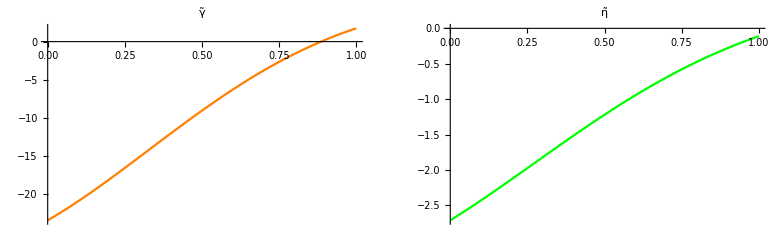

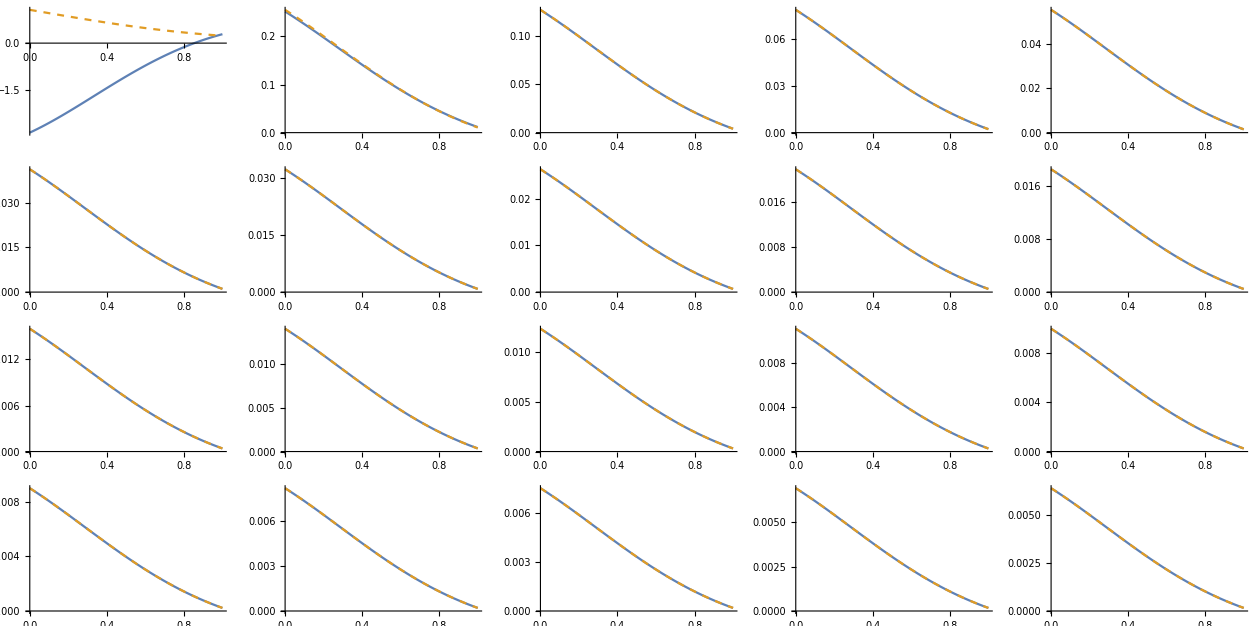

```mathematica
GraphicsGrid@{{Plot[γrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n],efV5[[n]]/(√(4π)r)},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
ψrTruelap[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
Determine[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,Tru,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
Tru=lap[efV5[[#]]/(√(4π)r),r]&/@REFRANGE;
REF=Tru/.r->r0;
RES=FindRoot[Thread[ψrTruelap[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTruelap[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}}/.RES
]
```

```mathematica
Determine[0.1]
```

FindRoot::precw: The precision of the argument function ({4 π (-4.67457157287644729496263129417×10^-6 γ-0.00025094891969046523109943283369 η)==-0.224373,4 π (-3.02917207210866187788554606878×10^-6 γ-0.000161498885164538217317213001234 η)==-0.144546}) is less than WorkingPrecision (30.).

{{0.1,574.629866228380314315817294028},{0.1,60.4461659640424327825247688115}}

```mathematica
Quiet@Module[{max=1,interval=0.01},
(*Zl=Determine[0][[1]];*)γllap={};ηllap={};
Monitor[Table[Module[{γη},
γη=Determine[r0];
(*AppendTo[Zl,γη[[1]]];*)
AppendTo[γllap,γη[[1]]];
AppendTo[ηllap,γη[[2]]];]
,{r0,0.01,max,interval}],Row[{ProgressIndicator[r0,{0,max}],100 r0/max"%"}]]
Print["End"]];
```

End

```mathematica
Export[$path<>"a="<>ToString[a]<>"γllapVs2V5.dat",γllap,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηllapVs2V5.dat",ηllap,"CSV"];
```

```mathematica
γrlap=Interpolation[γllap];
ηrlap=Interpolation[ηllap];
```

```mathematica
ψrfunlap[r_][n_]:=4π(γrlap[r] IntegrationVs21st[[n]]+ηrlap[r] a^2 IntegrationVs22nd[[n]])
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

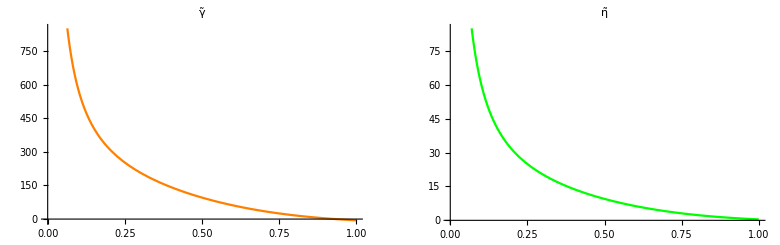

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

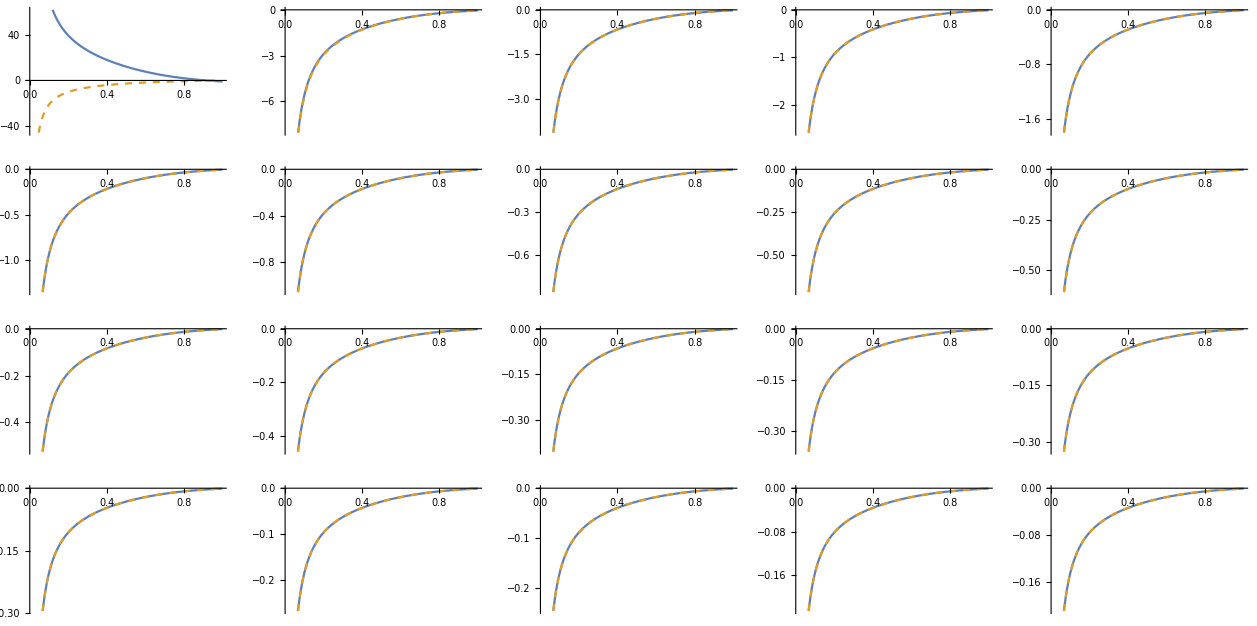

```mathematica
GraphicsGrid@{{Plot[γrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunlap[r][n],lapV5[[n]]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
Exit;
FrontEndExecute[FrontEndToken["EvaluateInitialization"]];
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
a=0.7;
```

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus9},{{c2,0},{d1,0}},MaxIterations->100,WorkingPrecision->30,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.62717616132991566940614778939 Power[«2»]-1.48020574106852906014836072679 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00031483920518654637477556119258663560362718871945) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.62717616132991566940614778939 Power[«2»]-1.48020574106852906014836072679 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00099560881683212171749909892753370933840725845078) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.62717616132991566940614778939 Power[«2»]-1.48020574106852906014836072679 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00031483920518654637477556119258663560362718871945) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {c2,d1} = {0.,0.}. Try perturbing the initial point(s).

{0.,0.}

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.46519,-0.18278,-0.0704256,-0.0371692,-0.0229357,-0.0155539,-0.0112382,-0.00849826,-0.00665075,-0.00534627,-0.0043911,-0.00367081,-0.00311424,-0.00267528,-0.002323,-0.00203598,-0.00179905,-0.00160119,-0.00143427,-0.00129214}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1388]-u''[r$1388]/2==e$1387 u[r$1388],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2210]-u''[r$2210]/2==e$2209 u[r$2210],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2410]-u''[r$2410]/2==e$2409 u[r$2410],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2340]-u''[r$2340]/2==e$2339 u[r$2340],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0371692169436628936433917867709}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2266]-u''[r$2266]/2==e$2265 u[r$2266],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00534626902950431127738123945136}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2488]-u''[r$2488]/2==e$2487 u[r$2488],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0229356945829587723666154636539}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2322]-u''[r$2322]/2==e$2321 u[r$2322],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.0112381718461354110738179614055}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2564]-u''[r$2564]/2==e$2563 u[r$2564],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0155539407576502234390353534216}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2382]-u''[r$2382]/2==e$2381 u[r$2382],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00439110366993289363567150763646}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2640]-u''[r$2640]/2==e$2639 u[r$2640],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{-0.0084982576130632855037793286084}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2626]-u''[r$2626]/2==e$2625 u[r$2626],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{-0.00311423641315441521148749791304}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2452]-u''[r$2452]/2==e$2451 u[r$2452],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00267528392834665967917961232085}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2586]-u''[r$2586]/2==e$2585 u[r$2586],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-0.00367080632701696886585475589417}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2810]-u''[r$2810]/2==e$2809 u[r$2810],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00665074688977182722711421595391}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2790]-u''[r$2790]/2==e$2789 u[r$2790],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.0017990477797848766487628268749}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2944]-u''[r$2944]/2==e$2943 u[r$2944],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00232299881260609958808458915997}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2728]-u''[r$2728]/2==e$2727 u[r$2728],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00143426581855186800466560951286}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2924]-u''[r$2924]/2==e$2923 u[r$2924],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00160119064190389155128879688607}

{-1.46519444532706110446965721253}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1444]-u''[r$1444]/2==e$1443 u[r$1444],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.0020359803403380249186919261358}

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00129214601794152124292028699125}

{-0.182780371354178358099564821575}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1500]-u''[r$1500]/2==e$1499 u[r$1500],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{-0.0704256294233960810980450764517}

{-1.46519444532706110446965721253,-0.182780371354178358099564821575,-0.0704256294233960810980450764517,-0.0371692169436628936433917867709,-0.0229356945829587723666154636539,-0.0155539407576502234390353534216,-0.0112381718461354110738179614055,-0.0084982576130632855037793286084,-0.00665074688977182722711421595391,-0.00534626902950431127738123945136,-0.00439110366993289363567150763646,-0.00367080632701696886585475589417,-0.00311423641315441521148749791304,-0.00267528392834665967917961232085,-0.00232299881260609958808458915997,-0.0020359803403380249186919261358,-0.0017990477797848766487628268749,-0.00160119064190389155128879688607,-0.00143426581855186800466560951286,-0.00129214601794152124292028699125}

```mathematica
Export[$path<>"a="<>ToString[a]<>"c2d1V5.dat",energyVs2,"CSV"];
```

```mathematica
Import["D:\\Documents\\aDependence\\a=1c2d1V5.dat"];
```

```mathematica
Abs@((energyVs2-enV5)/enV5)
```

{0.1148192632377409270920413044,0.00985770451156465399112449259,0.0023961527838361860094144885,0.00092094162394301850338459293,0.000446770116172516496682541,0.0002496042261571726506587808,0.0001533330893248938367489406,0.000100844403718614631082387,0.00006982431383054270420189987,0.00005032790117153990558266233,0.00003746420914796140703202468,0.0000286362495544981654700432,0.0000223776921598716359284541,0.0000178177930232391729653192,0.0000144172231291354619043817,0.0000118297604615264605063774,9.82620510239401080189057×10^-6,8.25071454206599480306525×10^-6,6.994809745523272114245×10^-6,5.9813970202449790607163×10^-6}

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.001},{}];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]];
```

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-1.46519444532706110446965721253 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0371692169436628936433917867709 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0112381718461354110738179614055 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00534626902950431127738123945136 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00439110366993289363567150763646 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0229356945829587723666154636539 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0084982576130632855037793286084 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.182780371354178358099564821575 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00367080632701696886585475589417 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0155539407576502234390353534216 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00665074688977182722711421595391 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0704256294233960810980450764517 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00311423641315441521148749791304 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00232299881260609958808458915997 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0017990477797848766487628268749 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00143426581855186800466560951286 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00267528392834665967917961232085 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0020359803403380249186919261358 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.62717616132991566940614778939 Power[«2»]+1.48020574106852906014836072679 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00160119064190389155128879688607 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

LinkObject::linkn: Argument LinkObject["C:\Program Files\Wolfram Research\Mathematica\10.4\WolframKernel.exe" -subkernel -noinit -wstp -noicon,748,6] in LinkReadyQ[LinkObject["C:\Program Files\Wolfram Research\Mathematica\10.4\WolframKernel.exe" -subkernel -noinit -wstp -noicon,748,6]] has an invalid LinkObject number; the link may be closed.

LinkObject::linkn: Argument LinkObject["C:\Program Files\Wolfram Research\Mathematica\10.4\WolframKernel.exe" -subkernel -noinit -wstp -noicon,748,6] in LinkRead[LinkObject["C:\Program Files\Wolfram Research\Mathematica\10.4\WolframKernel.exe" -subkernel -noinit -wstp -noicon,748,6],Hold] has an invalid LinkObject number; the link may be closed.

Kernels::rdead: Subkernel connected through KernelObject[3,local] appears dead.

Kernels::rdead: Subkernel connected through KernelObject[3,local,<defunct>] appears dead.

LaunchKernels::final: Cloning kernel KernelObject[3,local,<defunct>] failed.

$Aborted

#### ψ_r Vs_2

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=NLimit[efV5[[#]]/(√(4π)r),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
DetermineVs2[0]
```

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=DetermineVs2[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[2]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γlVs2V5.dat",γlVs2,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηlVs2V5.dat",ηlVs2,"CSV"];
```

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

```mathematica
ψrfunVs2[r_][n_]:=4π(γrVs2[r] IntegrationVs21st[[n]]+ηrVs2[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n],efV5[[n]]/(√(4π)r)},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
ψrTruelap[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
Determine[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,Tru,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
Tru=lap[efV5[[#]]/(√(4π)r),r]&/@REFRANGE;
REF=Tru/.r->r0;
RES=FindRoot[Thread[ψrTruelap[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTruelap[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}}/.RES
]
```

```mathematica
Determine[0.1]
```

```mathematica
Quiet@Module[{max=1,interval=0.01},
(*Zl=Determine[0][[1]];*)γllap={};ηllap={};
Monitor[Table[Module[{γη},
γη=Determine[r0];
(*AppendTo[Zl,γη[[1]]];*)
AppendTo[γllap,γη[[1]]];
AppendTo[ηllap,γη[[2]]];]
,{r0,0.01,max,interval}],Row[{ProgressIndicator[r0,{0,max}],100 r0/max"%"}]]
Print["End"]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γllapVs2V5.dat",γllap,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηllapVs2V5.dat",ηllap,"CSV"];
```

```mathematica
γrlap=Interpolation[γllap];
ηrlap=Interpolation[ηllap];
```

```mathematica
ψrfunlap[r_][n_]:=4π(γrlap[r] IntegrationVs21st[[n]]+ηrlap[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunlap[r][n],lapV5[[n]]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
Exit;
FrontEndExecute[FrontEndToken["EvaluateInitialization"]];
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
a=0.3;
```

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus9},{{c2,-40},{d1,3}},MaxIterations->100,WorkingPrecision->30,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"c2d1V5.dat",energyVs2,"CSV"];
```

```mathematica
Import["D:\\Documents\\aDependence\\a=1c2d1V5.dat"];
```

```mathematica
Abs@((energyVs2-enV5)/enV5)
```

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.001},{}];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]];
```

#### ψ_r Vs_2

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=NLimit[efV5[[#]]/(√(4π)r),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
DetermineVs2[0]
```

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=DetermineVs2[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[2]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γlVs2V5.dat",γlVs2,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηlVs2V5.dat",ηlVs2,"CSV"];
```

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

```mathematica
ψrfunVs2[r_][n_]:=4π(γrVs2[r] IntegrationVs21st[[n]]+ηrVs2[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n],efV5[[n]]/(√(4π)r)},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
ψrTruelap[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
Determine[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,Tru,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
Tru=lap[efV5[[#]]/(√(4π)r),r]&/@REFRANGE;
REF=Tru/.r->r0;
RES=FindRoot[Thread[ψrTruelap[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTruelap[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}}/.RES
]
```

```mathematica
Determine[0.1]
```

```mathematica
Quiet@Module[{max=1,interval=0.01},
(*Zl=Determine[0][[1]];*)γllap={};ηllap={};
Monitor[Table[Module[{γη},
γη=Determine[r0];
(*AppendTo[Zl,γη[[1]]];*)
AppendTo[γllap,γη[[1]]];
AppendTo[ηllap,γη[[2]]];]
,{r0,0.01,max,interval}],Row[{ProgressIndicator[r0,{0,max}],100 r0/max"%"}]]
Print["End"]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γllapVs2V5.dat",γllap,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηllapVs2V5.dat",ηllap,"CSV"];
```

```mathematica
γrlap=Interpolation[γllap];
ηrlap=Interpolation[ηllap];
```

```mathematica
ψrfunlap[r_][n_]:=4π(γrlap[r] IntegrationVs21st[[n]]+ηrlap[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunlap[r][n],lapV5[[n]]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
Exit;
FrontEndExecute[FrontEndToken["EvaluateInitialization"]];
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
a=0.1;
```

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus9},{{c2,-40},{d1,3}},MaxIterations->100,WorkingPrecision->30,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"c2d1V5.dat",energyVs2,"CSV"];
```

```mathematica
Import["D:\\Documents\\aDependence\\a=1c2d1V5.dat"];
```

```mathematica
Abs@((energyVs2-enV5)/enV5)
```

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.001},{}];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]];
```

#### ψ_r Vs_2

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=NLimit[efV5[[#]]/(√(4π)r),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
DetermineVs2[0]
```

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=DetermineVs2[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[2]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γlVs2V5.dat",γlVs2,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηlVs2V5.dat",ηlVs2,"CSV"];
```

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

```mathematica
ψrfunVs2[r_][n_]:=4π(γrVs2[r] IntegrationVs21st[[n]]+ηrVs2[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n],efV5[[n]]/(√(4π)r)},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
ψrTruelap[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
Determine[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,Tru,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
Tru=lap[efV5[[#]]/(√(4π)r),r]&/@REFRANGE;
REF=Tru/.r->r0;
RES=FindRoot[Thread[ψrTruelap[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTruelap[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}}/.RES
]
```

```mathematica
Determine[0.1]
```

```mathematica
Quiet@Module[{max=1,interval=0.01},
(*Zl=Determine[0][[1]];*)γllap={};ηllap={};
Monitor[Table[Module[{γη},
γη=Determine[r0];
(*AppendTo[Zl,γη[[1]]];*)
AppendTo[γllap,γη[[1]]];
AppendTo[ηllap,γη[[2]]];]
,{r0,0.01,max,interval}],Row[{ProgressIndicator[r0,{0,max}],100 r0/max"%"}]]
Print["End"]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γllapVs2V5.dat",γllap,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηllapVs2V5.dat",ηllap,"CSV"];
```

```mathematica
γrlap=Interpolation[γllap];
ηrlap=Interpolation[ηllap];
```

```mathematica
ψrfunlap[r_][n_]:=4π(γrlap[r] IntegrationVs21st[[n]]+ηrlap[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunlap[r][n],lapV5[[n]]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
Exit;
FrontEndExecute[FrontEndToken["EvaluateInitialization"]];
```